```mathematica
Subscript[p, 1]={Subscript[px, 1],Subscript[py, 1],Subscript[pz, 1]};
Subscript[v, 1]={Subscript[vx, 1],Subscript[vy, 1],Subscript[vz, 1]};
Subscript[r, 1]=a;
Subscript[p, 2]={Subscript[px, 2],Subscript[py, 2],Subscript[pz, 2]};
Subscript[v, 2]={Subscript[vx, 2],Subscript[vy, 2],Subscript[vz, 2]};
Subscript[r, 2]=b;
(Subscript[p, 1]+Subscript[v, 1] t)-(Subscript[p, 2]+Subscript[v, 2] t)==0
```

{px_1-px_2+t vx_1-t vx_2,py_1-py_2+t vy_1-t vy_2,pz_1-pz_2+t vz_1-t vz_2}==0

```mathematica
((Subscript[p, 1]+Subscript[v, 1] t)-(Subscript[p, 2]+Subscript[v, 2] t))^2
```

{(px_1-px_2+t vx_1-t vx_2)^2,(py_1-py_2+t vy_1-t vy_2)^2,(pz_1-pz_2+t vz_1-t vz_2)^2}

```mathematica
Total[((Subscript[p, 1]+Subscript[v, 1] t)-(Subscript[p, 2]+Subscript[v, 2] t))^2]
```

(px_1-px_2+t vx_1-t vx_2)^2+(py_1-py_2+t vy_1-t vy_2)^2+(pz_1-pz_2+t vz_1-t vz_2)^2

```mathematica
√Total[((Subscript[p, 1]+Subscript[v, 1] t)-(Subscript[p, 2]+Subscript[v, 2] t))^2]
```

√((px_1-px_2+t vx_1-t vx_2)^2+(py_1-py_2+t vy_1-t vy_2)^2+(pz_1-pz_2+t vz_1-t vz_2)^2)

```mathematica
√Total[((Subscript[p, 1]+Subscript[v, 1] t)-(Subscript[p, 2]+Subscript[v, 2] t))^2]==Subscript[r, 1]+Subscript[r, 2]
```

√((px_1-px_2+t vx_1-t vx_2)^2+(py_1-py_2+t vy_1-t vy_2)^2+(pz_1-pz_2+t vz_1-t vz_2)^2)==a+b

```mathematica
(Subscript[px, 1]-Subscript[px, 2]+t Subscript[vx, 1]-t Subscript[vx, 2])^2+(Subscript[py, 1]-Subscript[py, 2]+t Subscript[vy, 1]-t Subscript[vy, 2])^2+(Subscript[pz, 1]-Subscript[pz, 2]+t Subscript[vz, 1]-t Subscript[vz, 2])^2==(a+b)^2
```

(px_1-px_2+t vx_1-t vx_2)^2+(py_1-py_2+t vy_1-t vy_2)^2+(pz_1-pz_2+t vz_1-t vz_2)^2==(a+b)^2

```mathematica
dp=Subscript[p, 1]-Subscript[p, 2];
dv=Subscript[v, 1]-Subscript[v, 2];
(dp[[1]]+t dv[[1]])^2+(dp[[2]]+t dv[[2]])^2+(dp[[3]]+t dv[[3]])^2==(Subscript[r, 1]+Subscript[r, 2])^2
```

(px_1-px_2+t (vx_1-vx_2))^2+(py_1-py_2+t (vy_1-vy_2))^2+(pz_1-pz_2+t (vz_1-vz_2))^2==(a+b)^2

```mathematica
Subscript[p, 1]={-2,0,0};
Subscript[v, 1]={1,0,0};
Subscript[r, 1]=2;
Subscript[p, 2]={2,0,0};
Subscript[v, 2]={-1,0,0};
Subscript[r, 2]=1;
dp=Subscript[p, 1]-Subscript[p, 2];
dv=Subscript[v, 1]-Subscript[v, 2];
Solve[(dp[[1]]+t dv[[1]])^2+(dp[[2]]+t dv[[2]])^2+(dp[[3]]+t dv[[3]])^2-(Subscript[r, 1]+Subscript[r, 2])^2==0,t]
```

{{t→1/2},{t→7/2}}

{{t→1},{t→3}}

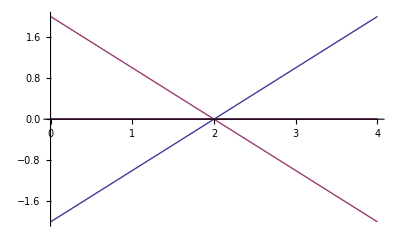

```mathematica
{{t->1},{t->3}}
Plot[{Subscript[p, 1]+Subscript[v, 1] t,Subscript[p, 2]+Subscript[v, 2] t},{t,0,4}]
```

```mathematica
Expand[(dp[[1]]+t dv[[1]])^2+(dp[[2]]+t dv[[2]])^2+(dp[[3]]+t dv[[3]])^2-(Subscript[r, 1]+Subscript[r, 2])^2,t]
```

16-(a+b)^2-16 t+4 t^2

```mathematica
Subscript[p, 1]={Subscript[px, 1],Subscript[py, 1],Subscript[pz, 1]};
Subscript[v, 1]={Subscript[vx, 1],Subscript[vy, 1],Subscript[vz, 1]};
Subscript[r, 1]=a;
Subscript[p, 2]={Subscript[px, 2],Subscript[py, 2],Subscript[pz, 2]};
Subscript[v, 2]={Subscript[vx, 2],Subscript[vy, 2],Subscript[vz, 2]};
Subscript[r, 2]=b;
dp=Subscript[p, 1]-Subscript[p, 2];
dv=Subscript[v, 1]-Subscript[v, 2];Collect[(dp[[1]]+t dv[[1]])^2+(dp[[2]]+t dv[[2]])^2+(dp[[3]]+t dv[[3]])^2-(Subscript[r, 1]+Subscript[r, 2])^2,t]
```

-(a+b)^2+px_1^2-2 px_1 px_2+px_2^2+py_1^2-2 py_1 py_2+py_2^2+pz_1^2-2 pz_1 pz_2+pz_2^2+t (2 px_1 (vx_1-vx_2)-2 px_2 (vx_1-vx_2)+2 py_1 (vy_1-vy_2)-2 py_2 (vy_1-vy_2)+2 pz_1 (vz_1-vz_2)-2 pz_2 (vz_1-vz_2))+t^2 ((vx_1-vx_2)^2+(vy_1-vy_2)^2+(vz_1-vz_2)^2)

```mathematica
dv^2
```

{(vx_1-vx_2)^2,(vy_1-vy_2)^2,(vz_1-vz_2)^2}

```mathematica
Total[dv^2]
```

(vx_1-vx_2)^2+(vy_1-vy_2)^2+(vz_1-vz_2)^2

```mathematica
2 Subscript[p, 1].dv
```

2 (px_1 (vx_1-vx_2)+py_1 (vy_1-vy_2)+pz_1 (vz_1-vz_2))

```mathematica
-2 Subscript[p, 1].Subscript[p, 2]
```

-2 (px_1 px_2+py_1 py_2+pz_1 pz_2)

```mathematica
-(a+b)^2+Subscript[px, 1]^2-2 Subscript[px, 1] Subscript[px, 2]+Subscript[px, 2]^2+Subscript[py, 1]^2-2 Subscript[py, 1] Subscript[py, 2]+Subscript[py, 2]^2+Subscript[pz, 1]^2-2 Subscript[pz, 1] Subscript[pz, 2]+Subscript[pz, 2]^2+t (2 Subscript[px, 1] (Subscript[vx, 1]-Subscript[vx, 2])-2 Subscript[px, 2] (Subscript[vx, 1]-Subscript[vx, 2])+2 Subscript[py, 1] (Subscript[vy, 1]-Subscript[vy, 2])-2 Subscript[py, 2] (Subscript[vy, 1]-Subscript[vy, 2])+2 Subscript[pz, 1] (Subscript[vz, 1]-Subscript[vz, 2])-2 Subscript[pz, 2] (Subscript[vz, 1]-Subscript[vz, 2]))+t^2 Total[dv^2]
```

-(a+b)^2+px_1^2-2 px_1 px_2+px_2^2+py_1^2-2 py_1 py_2+py_2^2+pz_1^2-2 pz_1 pz_2+pz_2^2+t (2 px_1 (vx_1-vx_2)-2 px_2 (vx_1-vx_2)+2 py_1 (vy_1-vy_2)-2 py_2 (vy_1-vy_2)+2 pz_1 (vz_1-vz_2)-2 pz_2 (vz_1-vz_2))+t^2 ((vx_1-vx_2)^2+(vy_1-vy_2)^2+(vz_1-vz_2)^2)

```mathematica
-(a+b)^2+Subscript[px, 1]^2-2 Subscript[p, 1].Subscript[p, 2]+Subscript[px, 2]^2+Subscript[py, 1]^2+Subscript[py, 2]^2+Subscript[pz, 1]^2+Subscript[pz, 2]^2+t (2 Subscript[p, 1].dv-2 Subscript[px, 2] (Subscript[vx, 1]-Subscript[vx, 2])-2 Subscript[py, 2] (Subscript[vy, 1]-Subscript[vy, 2])-2 Subscript[pz, 2] (Subscript[vz, 1]-Subscript[vz, 2]))+t^2 Total[dv^2]
```

-(a+b)^2+px_1^2+px_2^2+py_1^2+py_2^2+pz_1^2+pz_2^2-2 (px_1 px_2+py_1 py_2+pz_1 pz_2)+t (-2 px_2 (vx_1-vx_2)-2 py_2 (vy_1-vy_2)+2 (px_1 (vx_1-vx_2)+py_1 (vy_1-vy_2)+pz_1 (vz_1-vz_2))-2 pz_2 (vz_1-vz_2))+t^2 ((vx_1-vx_2)^2+(vy_1-vy_2)^2+(vz_1-vz_2)^2)

```mathematica
Total[Subscript[p, 1]^2+Subscript[p, 2]^2]
```

px_1^2+px_2^2+py_1^2+py_2^2+pz_1^2+pz_2^2

```mathematica
-(a+b)^2-2 Subscript[p, 1].Subscript[p, 2]+Total[Subscript[p, 1]^2+Subscript[p, 2]^2]+t (2 Subscript[p, 1].dv-2 Subscript[px, 2] (Subscript[vx, 1]-Subscript[vx, 2])-2 Subscript[py, 2] (Subscript[vy, 1]-Subscript[vy, 2])-2 Subscript[pz, 2] (Subscript[vz, 1]-Subscript[vz, 2]))+t^2 Total[dv^2]
```

-(a+b)^2+px_1^2+px_2^2+py_1^2+py_2^2+pz_1^2+pz_2^2-2 (px_1 px_2+py_1 py_2+pz_1 pz_2)+t (-2 px_2 (vx_1-vx_2)-2 py_2 (vy_1-vy_2)+2 (px_1 (vx_1-vx_2)+py_1 (vy_1-vy_2)+pz_1 (vz_1-vz_2))-2 pz_2 (vz_1-vz_2))+t^2 ((vx_1-vx_2)^2+(vy_1-vy_2)^2+(vz_1-vz_2)^2)

```mathematica
-Total[2 Subscript[p, 2] dv]
```

-2 px_2 (vx_1-vx_2)-2 py_2 (vy_1-vy_2)-2 pz_2 (vz_1-vz_2)

```mathematica
-(a+b)^2-2 Subscript[p, 1].Subscript[p, 2]+Total[Subscript[p, 1]^2+Subscript[p, 2]^2]+t (2 Subscript[p, 1].dv-Total[2 Subscript[p, 2] dv])+t^2 Total[dv^2]
```

-(a+b)^2+px_1^2+px_2^2+py_1^2+py_2^2+pz_1^2+pz_2^2-2 (px_1 px_2+py_1 py_2+pz_1 pz_2)+t (-2 px_2 (vx_1-vx_2)-2 py_2 (vy_1-vy_2)+2 (px_1 (vx_1-vx_2)+py_1 (vy_1-vy_2)+pz_1 (vz_1-vz_2))-2 pz_2 (vz_1-vz_2))+t^2 ((vx_1-vx_2)^2+(vy_1-vy_2)^2+(vz_1-vz_2)^2)